```mathematica
45
```

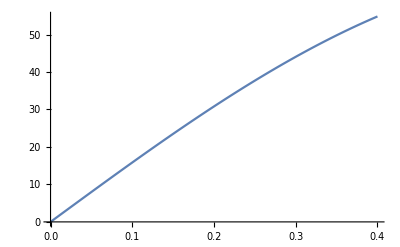

```mathematica
Plot[64Sin[2*x]+32*x*Cos[2*x],{x,0,0.4}]
```

```mathematica
64*Sin[2*0.4]+32*0.4*Cos[2*0.4]
```

54.8286

```mathematica
(54.82*(0.4)^4)/(4!)
```

0.0584747

```mathematica
2*(0.4)*Cos[2*0.4]-(0.4-2)^2
```

```mathematica
-2.002634632522268
```

```mathematica
2.016 -2.002634632522268
```

0.0133654

```mathematica
32/12
```

8/3

```mathematica
128+32
```

160

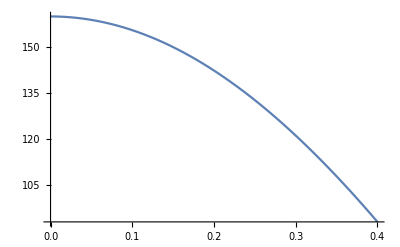

```mathematica
Plot[160Cos[2*x]-64*x*Sin[2*x],{x,0,0.4}]
```

```mathematica
(160*(0.4)^5)/(5!)
```

0.0136533

```mathematica
Expand[(1-x^2)*(x+2/3*x^3)]
```

x-x^3/3-(2 x^5)/3

```mathematica
Expand[(1-x^2+x^4/2)*(x+2/3*x^3+4/15*x^5)]
```

x-x^3/3+x^5/10+x^7/15+(2 x^9)/15

```mathematica
Expand[(1-x^2+x^4/2-x^6/6)*(x+2/3*x^3+4/15*x^5+8/105*x^7)]
```

x-x^3/3+x^5/10-x^7/42-(17 x^9)/315-(2 x^11)/315-(4 x^13)/315

```mathematica
2^4/(3*5*7*9)
```

16/945

```mathematica
Expand[(1-x^2+x^4/2-x^6/6+x^8/24)*(x+2/3*x^3+4/15*x^5+8/105*x^7+16/945*x^9)]
```

```mathematica
TeXForm[(1-x^2+x^4/2-x^6/6+x^8/24)*(x+2/3*x^3+4/15*x^5+8/105*x^7+16/945*x^9)]
```

\left(\frac{x^8}{24}-\frac{x^6}{6}+\frac{x^4}{2}-x^2+1\right) \left(\frac{16
   x^9}{945}+\frac{8 x^7}{105}+\frac{4 x^5}{15}+\frac{2 x^3}{3}+x\right)

```mathematica
TeXForm[x-x^3/3+x^5/10-x^7/42+x^9/216+(17 x^11)/3780+(13 x^13)/1890+x^15/2835+(2 x^17)/2835]
```

\frac{2 x^{17}}{2835}+\frac{x^{15}}{2835}+\frac{13 x^{13}}{1890}+\frac{17
   x^{11}}{3780}+\frac{x^9}{216}-\frac{x^7}{42}+\frac{x^5}{10}-\frac{x^3}{3}+x

```mathematica
x - x^3/3+x^5/10
```

```mathematica
Solve[2(0.5)^n==10^-6,n]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{n→20.9316}}

```mathematica
Sum[((-1)^k(2*k+1)!)/((2)(2k-n)!*k!),{k,0,∞}]
```

HypergeometricPFQ[{1,3/2},{1/2-n/2,1-n/2},-1]/(2 (-n)!)

```mathematica
FullSimplify[HypergeometricPFQ[{1/2,1},{1-n/2,3/2-n/2},-1]/((1-n)!)]
```

HypergeometricPFQ[{1/2,1},{1-n/2,3/2-n/2},-1]/Gamma[2-n]

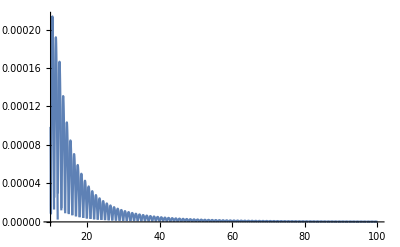

```mathematica
Plot[Abs[HypergeometricPFQ[{1/2,1},{1-n/2,3/2-n/2},-1]/((1-n)!*(n+1)!)],{n,10,100},PlotRange->All  ]
```

```mathematica
(π-3.1416)/π
```

-2.33843×10^-6

```mathematica
(ⅇ-2.718)/ⅇ
```

0.000103679

```mathematica
(√2-1.414)/(√2)
```

0.000151011

```mathematica
√2//N
```

1.41421

```mathematica
4/5//N
```

```mathematica
0.8`+0.333
```

0.8

```mathematica
(301/660-0.456)/(301/660)
```

0.00013289

```mathematica
0.800*0.333
```

0.2664

```mathematica
(1/3+3/11)-3/20
```

301/660

```mathematica
3/11//N
```

0.272727

```mathematica
3/20//N
```

0.15

```mathematica
0.333+0.273-0.150
```

0.456

```mathematica
2/(√π)*10^7//N
```

1.12838×10^7

```mathematica
fredy[k_]:=(2k+1)k!
```

```mathematica
Table[fredy[k],{k,8,10}]
```

{685440,6894720,76204800}

```mathematica
mitchell[y_] := 2/(√π)(1/((2y+1)y!))
```

```mathematica
Table[mitchell[t],{t,8,10}]
```

```mathematica
{1/(342720 √π),1/(3447360 √π),1/(38102400 √π)}//N
```

{1.64621×10^-6,1.63658×10^-7,1.48072×10^-8}

```mathematica
kirk=1/((2#+1)#!)&;
```

```mathematica
Table[{k,2/(√π)kirk[k]/10^-7//N//ScientificForm},{k,1,20}]//MatrixForm
```

(1 | 3.76126×10^6
2 | 1.12838×10^6
3 | 2.68662×10^5
4 | 5.22398×10^4
5 | 8.54833×10^3
6 | 1.20553×10^3
7 | 1.49257×10^2
8 | 1.64621×10^1
9 | 1.63658
10 | 1.48072×10^-1
11 | 1.22906×10^-2
12 | 9.42276×10^-4
13 | 6.71137×10^-5
14 | 4.46322×10^-6
15 | 2.78352×10^-7
16 | 1.63426×10^-8
17 | 9.06397×10^-10
18 | 4.76335×10^-11
19 | 2.37846×10^-12
20 | 1.13122×10^-13)

```mathematica
sum=0;
Do[sum+=1/n^2;
sum*=2;
,{n,1,10}]
```

```mathematica
sum
```

1968329/1270080

```mathematica
Sum[1/n^2,{n,1,10}]
```

1968329/1270080

```mathematica
NotebookDirectory[]
```

C:\Users\Mitchell\Documents\Numerical_analysis\

```mathematica
0.333+.272-.15
```

0.455

```mathematica
2/(√π)Sum[((-1)^k(1)^(2*k +1))/((2*k +1)k!),{k,0,10}]//N
```

0.842701

```mathematica
Erf[1]//N
```

0.842701

```mathematica
2/(√π)*ⅇ^(-(1^2))*Sum[2^k/((2*k+1)!!),{k,0,10}]//N
```

0.842701